# BDSTS.f

```mathematica
Func[x_]:=2(IntegerPart[x/2+0.1])-x+1/2
Potential[vBE_,vWS_,rWS_,aWS_,vLS_,rLS_,aLS_,vCoul_,vLsq_,r_]:=vBE-vWS/(1+Exp[(r-rWS)/aWS])-vLS/r Exp[(r-rLS)/aLS]/(1+Exp[(r-rLS)/aLS])^2+vCoul/r+vLsq/r^2
F1BDST[Rc_,x_,a5_,a6_]:=Piecewise[{{1/x,x≥ Rc},{a5+a6 x^2,x<Rc}}] (* Coulomb Potential *)

BDSTS[eb1i_,eb2i_,Vni_,Vsoi_, Rn_,An_,Rs_,As_,Rcoul_,Rmn_,Zn_,n_,l_,Ru_,h_,tol_,mode_]:=Module[
{eb1,eb2,Vn,Vso,Rmb,Zb,anL,ne,a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a910,a78,Rne,Rse,Rcoule,Rmu,eba,damp,vbs1,vbs2,vbs3,vbs4,vbs5,Rext,NRext,Rmax,NRmax,NRu,Rx,RecRx,Fr,Gr,PT,Rroot,Rcutoff,Rmtch,NRmtch,n1,n2,n3,n4,n5,b1,b2,b3,b4,b5,b6,Ybs,IP,Hsq,hd3,Icycle,Iter,Iubd1,Y,YD,F,Nod,SRul,SRulD,NRup1,NRx,src,RK1,s2,s3,Jcycle,IS,he,Inc,
nul,nulm3,kl,isrc,index1,index2 ,ENL,Rlmda},
{eb1,eb2,Vn,Vso}={eb1i,eb2i,Vni,Vsoi};
Rmb=1.0076;Zb=1;
anL=0;
ne=n-1;
a1=(Rmn-Rmb)^(1/3);
Rne=Rn a1;(* radius of Ucent B *)
Rse=Rs a1;(* radius of Uls B *)
Rcoule=Rcoul a1;
Rmu=(Rmn-Rmb) Rmb/Rmn;
(*Print["{anL,ne}"<>ToString[{anL,ne}]];
Print["{Rne,Rse,Rcoule,Rmu}"<>ToString[{Rne,Rse,Rcoule,Rmu}]];*)
a2=0.0478326 Rmu;
a3=2 a2 Vso/As;
If[mode==3,eb2=0];
If[mode==4,eb1=0];
a4=Max[1.5(Zn-Zb)Zb/Rcoule+200((ne+0.5(l+1))^2/(Rmu Rne^2)),5];
(*Print["{a1,a2,a3,a4}"<>ToString[{a1,a2,a3,a4}]];*)
If[Vn<0.0001,Vn=eb1+eb2+a4];
eba=eb1+eb2;
damp=Min[0.9,Max[0.1(Vn-eba)/eba,1.1 tol]];
(*Print["{eba,damp}"<>ToString[{eba,damp}]];*)
vbs1={a2 eb1,a2 eb2};
vbs2=a2 Vn;
vbs3={a3 l,-a3 l-a3};
vbs4=0.0688724 Rmu Zb (Zn-Zb);
vbs5=l(l+1);
(*Print["{vbs1,vbs2,vbs3,vbs4,vbs5}"<>ToString[{vbs1,vbs2,vbs3,vbs4,vbs5}]];*)

Rext=11.53 An +Rne;(*Print["Rext' = "<>ToString[Rext]];*)
NRext=IntegerPart[Rext/h+0.5];
If[Func[NRext]≤0, NRext = NRext+1];
Rext=NRext h;
Print["Rext = "<>ToString[Rext]];

Rmax=Max[Ru,2 Rext];(*Print["Rmax' = "<>ToString[Rmax]];*)
NRmax=IntegerPart[Rmax/h+0.5];
If[Func[NRmax]≤0,NRmax=NRmax+1];
Rmax=NRmax h;
Print["Rmax = "<>ToString[Rmax]];

NRu=IntegerPart[Ru/h+0.5];
If[Func[NRu]≤0,NRu=NRu+1];
(*Print["NRu = "<>ToString[NRu]];*)

a5=1.5/Rcoule;
a6=-0.5/Rcoule^3;
a7={Exp[h/An],Exp[h/As]};
a8={1/a7[[1]],1/a7[[2]]};
a9={Exp[-Rne/An],Exp[-Rse/As]};
a10={Exp[(Rext-Rne)/An],Exp[(Rext-Rse)/As]};
(*Print["{a5,a6,a7,a8,a9,a10}"<>ToString[{a5,a6,a7,a8,a9,a10}]];*)

Rx=Rext;
a910={a10[[1]],a10[[2]]};
(*Print["{Rctoff,Rx,a910}"<>ToString[{Max[Rne,Rcoule],Rx,a910}]];*)

Print[
Plot[Potential[vbs1[[1]]+vbs1[[2]],vbs2,Rne,An,Total[vbs3],Rse,As,vbs4,vbs5,x],{x,1,Rmax},PlotRange->All]
];
Rmtch=Max[
Rroot=x/.FindRoot[Potential[vbs1[[1]]+vbs1[[2]],vbs2,Rne,An,Total[vbs3],Rse,As,vbs4,vbs5,x]==0,{x,Rne}],
Rcutoff=Max[Rne,Rcoule]
];(*
Label[findRmtch];Rx=Rx-h;
If[Rx> Max[Rne,Rcoule],
RecRx=1/Rx;
a910={a910[[1]]a8[[1]],a910[[2]]a8[[2]]};
Fr=1/(1+a910[[1]]);
Gr=RecRx a910[[2]]/(1+a910[[2]])^2;
PT=vbs1[[1]]+vbs1[[2]]-vbs2 Fr-Total[vbs3]Gr+vbs4 RecRx+vbs5 RecRx^2;
(*Print["{Rx,PT}"<>ToString[{Rx,PT}]];*)
If[PT≤ 0,Rmtch=Rx, Goto[findRmtch]];,
Rmtch=Rx;
];*)
NRmtch=IntegerPart[Rmtch/h+0.5];
If[Func[NRmtch]≤0,NRmtch=NRmtch+1];
Rmtch=NRmtch h;
Print["{Rroot,Rcutoff, Rmtch} = "<>ToString[{Rroot,Rcutoff,Rmtch}]];


n1=NRmtch;
n2=NRext-NRmtch;
n3=NRmax-NRext;
If[mode==3,n4=1;n5=1;];
If[mode==4,n4=2;n5=2;];
(*Print["{n1,n2,n3,n4,n5}"<>ToString[{n1,n2,n3,n4,n5}]];*)

b5={{0,0},{0,0}};
IP=NRu+1;
Ybs={Table[0,{i,1,IP}],Table[0,{i,1,IP}]};

Do[
Ybs[[i,2]]=(-1)^ne h^(l+1);
,{i,n4,n5}];

Hsq=h^2;
hd3=h/3;
Icycle=0;
Iter=-1;
Iubd1=0;

(*vbs1={a2 eb1,a2 eb2};*)
b1={0,0};
b2={0,0};
b3={{0,0},{0,0}};
b4={0,0};
b5={{0,0},{0,0}};
b6={{0,0},{0,0}};
F=Table[0,{i,1,2},{j,1,7}];
Nod={0,0};
Y={{0,0},{0,0}};
YD={{0,0},{0,0}};
SRul={{{0,0},{0,0}},{{0,0},{0,0}}};
SRulD=Table[0,{i,1,8}];
Rlmda={0,0};

Rx=Rmax;
Table[
b1[[i]]=√vbs1[[i]];
b2[[i]]=0.5 vbs4/b1[[i]];
s2=1;
s3=1;
F[[i,3]]=s3 Exp[-b1[[i]] Rx-b2[[i]] Log[2 b1[[i]] Rx]];
F[[i,2]]=s2 Exp[-b1[[i]](Rx-h)-b2[[i]]Log[2 b1[[i]](Rx-h)]];
b4[[i]]=0;
If[NRmax≤ NRu,
Ybs[[i,NRmax+1]]=F[[i,3]];
Ybs[[i,NRmax]]=F[[i,2]];
];
,{i,n4,n5}];
(*Print[{"Ybs",Ybs}];
Print[{"F",F}];*)

(*Print["{NRext, NRmax = NRx, NRu, NRmtch}"<>ToString[{NRext, NRmax,NRu, NRmtch}]];*)
NRup1=NRu+1;
NRx=NRmax;
src=4.0;
(*Print[{"Rx",Rx}];*)
Table[
Rx=Rmax-i h;
(*RecRx=1/Rx;*)
NRx=NRmax-i;
RK1=vbs4/Rx+vbs5/Rx^2;
Table[
b1[[j]]=RK1+vbs1[[j]];
F[[j,1]]=(2+h^2 b1[[j]])F[[j,2]]-F[[j,3]];
If[NRx≤ NRup1,Ybs[[j,NRx]]=F[[j,1]]];
b4[[j]]=b4[[j]]+src (F[[j,2]])^2;
F[[j,3]]=F[[j,2]];
F[[j,2]]=F[[j,1]];
,{j,n4,n5}];
(*Print[{i,"src, Rx, NRx", src, Rx, NRx}];*)
src=6-src;
,{i,1,n3}];
(*Print[{"b1, b4",b1,b4}];
Print[{"Ybs",Ybs}];
Print[{"F",F}];*)



Do[
b6[[i,2]]=F[[i,3]];
b6[[i,1]]=F[[i,2]];
b4[[i]]=h/3(b4[[i]]-F[[i,3]]^2);
,{i,n4,n5}];
(*Print[{"b6, b4", b6, b4}];*)

Label[Loop78];(*Print["Loop78"];*)
Jcycle=0;
Lable[Loop79];(*Print["Loop79"];*)
(*Print[{"vbs2",vbs2,"a3",a3,"vbs3",vbs3}];*)
vbs2=a2 Vn;
a3=2 a2 Vso/As;
vbs3={a3 l, -a3 l -a3};

Table[
IS;
src=4.0;
If[IS≤ 1.5,
a78=a7;
a910=a9;
Rx=0;
he=h;
NRx=2;
Inc=1;
nul=n1+2;
nulm3=nul-3;
kl=5;
isrc=1;
index1=0;
index2=2;
Table[
F[[i,6]]=Ybs[[i,1]];
F[[i,7]]=Ybs[[i,2]];
SRulD[[index1+i]]=0;
,{i,n4,n5}];
];
If[IS> 1.5,
a78=a8;
a910=a10;
Rx=Rext;
he=-h;
NRx=NRext;
Inc=-1;
nul=n2+2;
nulm3=nul-3;
kl=5;
isrc=1;
index1=4;
index2=6;
Table[
F[[i,6]]=b6[[i,2]];
F[[i,7]]=b6[[i,1]];
SRulD[[index1+i]]=0;
SRulD[[index2+i]]=0;
,{i,n4,n5}];
];

(*Print[{"====================IS", IS, "Rx", Rx, "nul", nul}];*)
(*Print[{"F",F}];*)
(*Print[{"he",he,"inc",Inc, "a78",a78,"a910",a910}];*)

Do[
Rx=Rx+he;
NRx=NRx+Inc;
a910={a910[[1]]a78[[1]],a910[[2]]a78[[2]]};
Fr=1/(1+a910[[1]]);
Gr=1/Rx a910[[2]]/(1+a910[[2]])^2;
RK1=-vbs2 Fr + vbs5/Rx^2;
(*Print[{"RK1 b4:", RK1,"vbs2", vbs2,"vbs5",vbs5,"Rx",Rx, "F1BDST",F1BDST[Rcoule,Rx,a5,a6]}];*)
If[IS≤ 1.5,
RK1=RK1+vbs4 F1BDST[Rcoule,Rx,a5,a6];,
RK1=RK1+vbs4/Rx;
];
If[nulm3≤ i,
kl=kl-1;
isrc=isrc-1;
];

(*Print[{"a910",a910,"Fr",Fr,"Gr",Gr,"RK1",RK1}];*)

Do[
(*Print[{"=========i",i,,"nulm3",nulm3,"kl,",kl, "F b4", F}];*)
Do[F[[j,k]]=F[[j,k+1]],{k,kl,6}];
(*Print[{"F af", F}];*)
b1[[j]]=RK1+vbs1[[j]]-vbs3[[j]] Gr;
F[[j,7]]=(2+h^2 b1[[j]])F[[j,6]]-F[[j,5]];
(*Print[{"F end", F}];*)
If[IS<1.5 && F[[j,6]]F[[j,5]]<0, Nod[[j]]=Nod[[j+1]]];
b2[[j]]=src (   F[[j,6]]  )^2;
If[Iter≥0, 
ENL=1;
If[NRx≤ NRu+1, Ybs[[j,NRx]]=F[[j,7]] ENL];
b5[[j,IS]]=b5[[j,IS]]+b2[[j]] ENL^2;
];
SRulD[[index1+j]]=SRulD[[index1+j]] + vbs2 Fr b2[[j]];
,{j,n4,n5}];
(*Print[{"b1", b1, "b2", b2, "b5",b5, "SRulD", SRulD}];*)

If[isrc<0, src=0];
If[isrc==0, src=1];
If[isrc>0, src=6-src];
,{i,1,nul}];
Do[
Y[[i,IS]]=F[[i,4]];
YD[[i,IS]]=(0.01666666667(F[[i,7]]-F[[i,1]])+0.15(F[[i,2]]-F[[i,6]])+0.75(F[[i,5]]-F[[i,3]]))/he;
If[Iter>0,b5[[i,IS]]=h/3 b5[[i,IS]]];
SRul[[i,1,IS]]=h/3 SRulD[[index1+i]];
,{i,n4,n5}];
(*Print[{"F", F}];*)
,{IS,1,2}];
(*Print[{"******************************** iter", Iter}];
Print[{"Y",Y}];
Print[{"YD",YD}];
Print[{"Rlmda",Rlmda}];*)
If[Iter≤0,
Do[
If[ne<Nod[[i]] || ne > Nod[[i]], 
Jcycle=Jcycle+1;
If[Jcycle≤5,
Vn=Abs[Vn+5Sign[ne-Nod[[n4]]]];
Print["Goto:Loop79"];
Goto[Loop79];,
Print["STOP ne = Nod"];
Return[];
],
Break[];
];
,{i,n4,n5}];
Do[
b1[[i]]=(Y[[i,2]]/Y[[i,1]])^2;
b2[[i]]=Y[[i,2]]YD[[i,2]]-Y[[i,1]]YD[[i,1]]b1[[i]];
,{i,n4,n5}];

Icycle=Icycle+1;

If[Icycle>20,
FFF=Max[Abs[Rlmda]];
Iter = Iter+2;
Print["STOP Icylce>20"];Return[];
];
If[Icycle≤20,
Rlmda={b2[[n4]]/(b1[[n4]]SRul[[n4,1,1]]+SRul[[n4,1,2]]),0};
If[Max[Abs[Rlmda]]≥1,
Iubd1=Iubd1+1;
If[Iubd1>5, Print["STOP Iubd1>5"];Return[];]
];
If[Abs[Rlmda[[1]]]>damp,Rlmda[[1]]=damp Sign[Rlmda[[1]]];];
If[Abs[Rlmda[[2]]]>damp,Rlmda[[2]]=damp Sign[Rlmda[[2]]];];
Vn=(1-Rlmda[[1]])Vn;
Vso=(1-Rlmda[[2]])Vso;
Print[{"Icycle",Icycle,"Vn,Vso,eb1,eb2",Vn,Vso,eb1,eb2}];
(*Print[{"Rlmda",Rlmda}];*)
If[Abs[Rlmda[[1]]]≤ tol && Abs[Rlmda[[2]]]≤ tol, Iter=Iter+2;];
(*Print["Goto:Loop78"];*)
Goto[Loop78];
];
]
If[Iter>0,
nul=Min[n1-3,NRup1];
Print[{"Final Val", "Vn,Vso,eb1,eb2",Vn,Vso,eb1,eb2}];
Do[
b1[[i]]=Y[[i,2]]/Y[[i,1]];
b5[[i,1]]=b1[[i]] b1[[i]] b5[[i,1]];
b2[[i]]=√(1/(b5[[i,1]]+b5[[i,2]]+b4[[i]]));
b4[[i]]=b1[[i]] b2[[i]];
(*Print[{"b1,b2,b5,b4", b1,b2,b5,b4}];*)
Do[
Ybs[[i,j]]=b4[[i]] Ybs[[i,j]];
,{j,1,nul}];
IP=nul+1;
Do[
Ybs[[i,j]]=b2[[i]]Ybs[[i,j]];
,{j,IP,NRup1}];
,{i,n4,n5}];
];
Table[{(i-1) h,Ybs[[n4,i]]},{i,1,NRu}]
]
```

Rext = 11.4

Rmax = 22.8

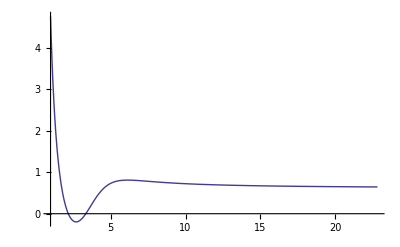

{Rroot,Rcutoff, Rmtch} = {3.35072, 3.55818, 3.6}

{Icycle,1,Vn,Vso,eb1,eb2,69.8684,12,0,13.26}

{Icycle,2,Vn,Vso,eb1,eb2,78.0578,12,0,13.26}

{Icycle,3,Vn,Vso,eb1,eb2,76.4372,12,0,13.26}

{Icycle,4,Vn,Vso,eb1,eb2,76.271,12,0,13.26}

{Icycle,5,Vn,Vso,eb1,eb2,76.2696,12,0,13.26}

{Final Val,Vn,Vso,eb1,eb2,76.2696,12,0,13.26}

{{0.,0.},{0.1,0.000146855},{0.2,0.00117135},{0.3,0.0039237},{0.4,0.0091928},{0.5,0.017676},{0.6,0.0299523},{0.7,0.0464601},{0.8,0.0674795},{0.9,0.0931204},{1.,0.123316},{1.1,0.157825},{1.2,0.196234},{1.3,0.237974},{1.4,0.282338},{1.5,0.328504},{1.6,0.375563},{1.7,0.42255},{1.8,0.468478},{1.9,0.512376},{2.,0.553316},{2.1,0.590453},{2.2,0.623049},{2.3,0.650497},{2.4,0.672344},{2.5,0.688301},{2.6,0.698243},{2.7,0.702214},{2.8,0.700411},{2.9,0.693171},{3.,0.680948},{3.1,0.664287},{3.2,0.643796},{3.3,0.620122},{3.4,0.593914},{3.5,0.565815},{3.6,0.536424},{3.7,0.506296},{3.8,0.475923},{3.9,0.445732},{4.,0.416078},{4.1,0.387252},{4.2,0.359478},{4.3,0.332924},{4.4,0.307705},{4.5,0.283892},{4.6,0.261519},{4.7,0.24059},{4.8,0.221085},{4.9,0.202966},{5.,0.18618},{5.1,0.170668},{5.2,0.156361},{5.3,0.143188},{5.4,0.131078},{5.5,0.119958},{5.6,0.109758},{5.7,0.10041},{5.8,0.0918483},{5.9,0.0840121},{6.,0.0768429},{6.1,0.0702863},{6.2,0.0642915},{6.3,0.0588117},{6.4,0.0538032},{6.5,0.0492259},{6.6,0.0450429},{6.7,0.0412203},{6.8,0.0377268},{6.9,0.034534},{7.,0.0316158},{7.1,0.0289482},{7.2,0.0265096},{7.3,0.0242799},{7.4,0.022241},{7.5,0.0203763},{7.6,0.0186707},{7.7,0.0171103},{7.8,0.0156825},{7.9,0.014376},{8.,0.0131801},{8.1,0.0120854},{8.2,0.0110831},{8.3,0.0101652},{8.4,0.00932461},{8.5,0.0085546},{8.6,0.00784916},{8.7,0.00720277},{8.8,0.00661041},{8.9,0.00606746},{9.,0.00556975},{9.1,0.00511344},{9.2,0.00469502},{9.3,0.00431131},{9.4,0.00395936},{9.5,0.00363651},{9.6,0.00334032},{9.7,0.00306855},{9.8,0.00281916},{9.9,0.00259028},{10.,0.0023802},{10.1,0.00218735},{10.2,0.00201029},{10.3,0.00184772},{10.4,0.00169844},{10.5,0.00156135},{10.6,0.00143543},{10.7,0.00131977},{10.8,0.00121352},{10.9,0.00111591},{11.,0.00102622},{11.1,0.000943807},{11.2,0.000868071},{11.3,0.000798466},{11.4,0.000734491},{11.5,0.000675685},{11.6,0.000621627},{11.7,0.000571928},{11.8,0.000526235},{11.9,0.000484222},{12.,0.000445588},{12.1,0.00041006},{12.2,0.000377386},{12.3,0.000347334},{12.4,0.000319692},{12.5,0.000294266},{12.6,0.000270876},{12.7,0.000249357},{12.8,0.00022956},{12.9,0.000211344},{13.,0.000194583},{13.1,0.00017916},{13.2,0.000164967},{13.3,0.000151905}}

```mathematica
BState=BDSTS[0,13.26,0,12, 1.27,0.67,1.27,0.67,1.25,23,9,1,2,13.4,0.1,0.001,4]
```

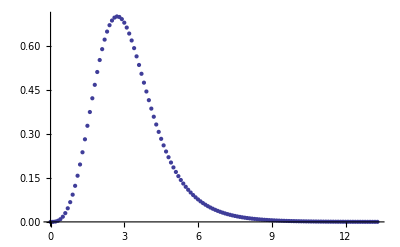

3.05377

```mathematica
ListPlot[BState]
√Sum[(BState[[i,1]]BState[[i,2]])^2 0.1,{i,1,Length[BState]}]
```